## Nieuwenhuizen Operators Algebra

```mathematica
<<FeynGrav`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynGrav: All expressions for itteraction veritce are evaluated on a call.

FeynGrav: Please, be patient. Evaluation can take some time.

FeynGrav: FeynGravCommands print the list of all supported commands.

FeynGrav: Use '?CommandName' to see a brief description.

```mathematica
?NieuwenhuizenOperator1
?NieuwenhuizenOperator2
?NieuwenhuizenOperator0
?NieuwenhuizenOperator0Bar
?NieuwenhuizenOperator0BarBar
```

```mathematica
NieuwenhuizenOperator1[μ,ν,α,β,p]
NieuwenhuizenOperator2[μ,ν,α,β,p]
NieuwenhuizenOperator0[μ,ν,α,β,p]
NieuwenhuizenOperator0Bar[μ,ν,α,β,p]
NieuwenhuizenOperator0BarBar[μ,ν,α,β,p]
```

1/2 ((p^β p^ν (g^αμ-(p^α p^μ)/p^2))/p^2+(p^α p^ν (g^βμ-(p^β p^μ)/p^2))/p^2+(p^β p^μ (g^αν-(p^α p^ν)/p^2))/p^2+(p^α p^μ (g^βν-(p^β p^ν)/p^2))/p^2)

1/2 ((g^αν-(p^α p^ν)/p^2) (g^βμ-(p^β p^μ)/p^2)+(g^αμ-(p^α p^μ)/p^2) (g^βν-(p^β p^ν)/p^2))-1/3 (g^αβ-(p^α p^β)/p^2) (g^μν-(p^μ p^ν)/p^2)

1/3 (g^αβ-(p^α p^β)/p^2) (g^μν-(p^μ p^ν)/p^2)

(p^α p^β p^μ p^ν)/p^4

(p^μ p^ν (g^αβ-(p^α p^β)/p^2))/p^2+(p^α p^β (g^μν-(p^μ p^ν)/p^2))/p^2

```mathematica
Evaluate[Calc[NieuwenhuizenOperator0[μ,ν,ρ,σ,p]NieuwenhuizenOperator1[ρ,σ,α,β,p]]/.D->4]==0
Evaluate[Calc[NieuwenhuizenOperator1[μ,ν,ρ,σ,p]NieuwenhuizenOperator2[ρ,σ,α,β,p]]/.D->4]==0
Evaluate[Calc[NieuwenhuizenOperator0[μ,ν,ρ,σ,p]NieuwenhuizenOperator2[ρ,σ,α,β,p]]/.D->4]==0
Evaluate[Calc[NieuwenhuizenOperator0[μ,ν,ρ,σ,p]NieuwenhuizenOperator0[ρ,σ,α,β,p]==NieuwenhuizenOperator0[μ,ν,α,β,p]]/.D->4]
Evaluate[Calc[NieuwenhuizenOperator1[μ,ν,ρ,σ,p]NieuwenhuizenOperator1[ρ,σ,α,β,p]==NieuwenhuizenOperator1[μ,ν,α,β,p]]/.D->4]
Evaluate[Calc[NieuwenhuizenOperator2[μ,ν,ρ,σ,p]NieuwenhuizenOperator2[ρ,σ,α,β,p]==NieuwenhuizenOperator2[μ,ν,α,β,p]]/.D->4]
Evaluate[Calc[NieuwenhuizenOperator0BarBar[μ,ν,ρ,σ,p]NieuwenhuizenOperator0[ρ,σ,α,β,p]+NieuwenhuizenOperator0[μ,ν,ρ,σ,p]NieuwenhuizenOperator0BarBar[ρ,σ,α,β,p]==NieuwenhuizenOperator0BarBar[μ,ν,α,β,p]]/.D->4]
Evaluate[Calc[NieuwenhuizenOperator0BarBar[μ,ν,ρ,σ,p]NieuwenhuizenOperator1[ρ,σ,α,β,p]==0]/.D->4]
Evaluate[Calc[NieuwenhuizenOperator0BarBar[μ,ν,ρ,σ,p]NieuwenhuizenOperator2[ρ,σ,α,β,p]==0]/.D->4]
Evaluate[Calc[NieuwenhuizenOperator0Bar[μ,ν,ρ,σ,p]NieuwenhuizenOperator0[ρ,σ,α,β,p]==0]/.D->4]
Evaluate[Calc[NieuwenhuizenOperator0Bar[μ,ν,ρ,σ,p]NieuwenhuizenOperator1[ρ,σ,α,β,p]==0]/.D->4]
Evaluate[Calc[NieuwenhuizenOperator0Bar[μ,ν,ρ,σ,p]NieuwenhuizenOperator2[ρ,σ,α,β,p]==0]/.D->4]
Evaluate[Calc[NieuwenhuizenOperator0Bar[μ,ν,ρ,σ,p]NieuwenhuizenOperator0Bar[ρ,σ,α,β,p]==NieuwenhuizenOperator0Bar[μ,ν,α,β,p]]/.D->4]
Evaluate[Calc[NieuwenhuizenOperator0BarBar[μ,ν,ρ,σ,p]NieuwenhuizenOperator0BarBar[ρ,σ,α,β,p]==3NieuwenhuizenOperator0[μ,ν,α,β,p]+3 NieuwenhuizenOperator0Bar[μ,ν,α,β,p]]/.D->4]
Evaluate[Calc[NieuwenhuizenOperator0BarBar[μ,ν,ρ,σ,p]NieuwenhuizenOperator0Bar[ρ,σ,α,β,p]+NieuwenhuizenOperator0Bar[μ,ν,ρ,σ,p]NieuwenhuizenOperator0BarBar[ρ,σ,α,β,p]==NieuwenhuizenOperator0BarBar[μ,ν,α,β,p]]/.D->4]
```

True

True

True

«12 more identical outputs»

## 2->2 tree level graviton scattering

```mathematica
<<FeynGrav`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynGrav: All expressions for itteraction veritce are evaluated on a call.

FeynGrav: Please, be patient. Evaluation can take some time.

FeynGrav: FeynGravCommands print the list of all supported commands.

FeynGrav: Use '?CommandName' to see a brief description.

S-amplitude

```mathematica
ℳs[μ1_,ν1_,μ2_,ν2_,μ3_,ν3_,μ4_,ν4_,p1_,p2_,p3_,p4_]=Calc[GravitonVertex[μ1,ν1,p1,μ2,ν2,p2,α1,β1,-p1-p2]GravitonPropagatorAlternative[α1,β1,α2,β2,p1+p2]GravitonVertex[μ3,ν3,p3,μ4,ν4,p4,α2,β2,p1+p2]];//Timing
```

{186.198,Null}

Kinematics

```mathematica
SetMandelstam[s,t,u,p1,p2,p3,p4,0,0,0,0];
Pair[Momentum[Polarization[p1,ⅈ]],Momentum[Polarization[p1,ⅈ]]]=Pair[Momentum[Polarization[p2,ⅈ]],Momentum[Polarization[p2,ⅈ]]]=Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]=Pair[Momentum[Polarization[p4,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]=0;
Pair[Momentum[p1],Momentum[Polarization[p1,ⅈ]]]=Pair[Momentum[p2],Momentum[Polarization[p2,ⅈ]]]=Pair[Momentum[p3],Momentum[Polarization[p3,-ⅈ]]]=Pair[Momentum[p4],Momentum[Polarization[p4,-ⅈ]]]=0;
Pair[Momentum[Polarization[p1,ⅈ]],Momentum[Polarization[p2,ⅈ]]]=(1+h1 h2)/2;
Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]=(1+h3 h4)/2;
Pair[Momentum[Polarization[p1,ⅈ]],Momentum[Polarization[p3,-ⅈ]]]=1/(2 s)(s+h1 h3 (s+2 t));
Pair[Momentum[Polarization[p2,ⅈ]],Momentum[Polarization[p4,-ⅈ]]]=1/(2 s)(s+h2 h4 (s+2 t));
Pair[Momentum[Polarization[p1,ⅈ]],Momentum[Polarization[p4,-ⅈ]]]=1/(2 s)h1 h4 (h1 h4 s-t+u);
Pair[Momentum[Polarization[p2,ⅈ]],Momentum[Polarization[p3,-ⅈ]]]=1/(2 s)h3 h2 (h3 h2 s-t+u);
Pair[Momentum[p1],Momentum[Polarization[p2,ⅈ]]]=Pair[Momentum[p2],Momentum[Polarization[p1,ⅈ]]]=Pair[Momentum[p3],Momentum[Polarization[p4,-ⅈ]]]=Pair[Momentum[p4],Momentum[Polarization[p3,-ⅈ]]]=0;
Pair[Momentum[p1],Momentum[Polarization[p3,-ⅈ]]]=h3 √((t u)/(2 s));
Pair[Momentum[p2],Momentum[Polarization[p4,-ⅈ]]]=h4 √((t u)/(2 s));
Pair[Momentum[p3],Momentum[Polarization[p2,ⅈ]]]=h2 √((t u)/(2 s));
Pair[Momentum[p4],Momentum[Polarization[p1,ⅈ]]]=h1 √((t u)/(2 s));
Pair[Momentum[p1],Momentum[Polarization[p4,-ⅈ]]]=-h4  √((t u)/(2 s));
Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]]=-h3  √((t u)/(2 s));
Pair[Momentum[p3],Momentum[Polarization[p1,ⅈ]]]=-h1 √((t u)/(2 s));
Pair[Momentum[p4],Momentum[Polarization[p2,ⅈ]]]=-h2  √((t u)/(2 s));
PolarizationTensor[m1_,n1_,m2_,n2_,m3_,n3_,m4_,n4_,p1_,p2_,p3_,p4_]=Pair[LorentzIndex[m1],Momentum[Polarization[p1,ⅈ]]]Pair[LorentzIndex[n1],Momentum[Polarization[p1,ⅈ]]]Pair[LorentzIndex[m2],Momentum[Polarization[p2,ⅈ]]]Pair[LorentzIndex[n2],Momentum[Polarization[p2,ⅈ]]]Pair[LorentzIndex[m3],Momentum[Polarization[p3,-ⅈ]]]Pair[LorentzIndex[n3],Momentum[Polarization[p3,-ⅈ]]]Pair[LorentzIndex[m4],Momentum[Polarization[p4,-ⅈ]]]Pair[LorentzIndex[n4],Momentum[Polarization[p4,-ⅈ]]];
$Assumptions=h1^2==h2^2==h3^2==h4^2==1&&s+t+u==0&&Element[s|t|u,Reals];
```

s-channel

```mathematica
AmplitudeSChannel = Calc[Evaluate[ℳs[μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4,p1,p2,p3,p4]/.D->4]PolarizationTensor[μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4,p1,p2,p3,p4]];//Timing
TrickMandelstam[AmplitudeSChannel,{s,t,u,0}]//Simplify
```

{49.4807,Null}

(9 ⅈ κ^2 t u (h1 h2+1) (h3 h4+1))/(16 s)

t-channel

```mathematica
AmplitudeTChannel = Calc[Evaluate[ℳs[μ1,ν1,μ3,ν3,μ2,ν2,μ4,ν4,p1,p3,p2,p4]/.D->4]PolarizationTensor[μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4,p1,p2,p3,p4]];//Timing
TrickMandelstam[AmplitudeTChannel,{s,t,u,0}]//Simplify
```

{60.1459,Null}

(ⅈ κ^2 u (t^4 (h1 h3-1) (h2 h4-1)+2 t^3 u (h1 (2 h2 h3 h4+h2+h3+h4)+h2 (h3+h4)+h3 h4)+6 t^2 u^2 (h1 (h2 h3 h4+h2+h3+h4)+h2 (h3+h4)+h3 h4+1)+4 t u^3 (h1 (h2 h3 h4+h2+h3+h4)+h2 (h3+h4)+h3 h4+1)+u^4 (h1 h3+1) (h2 h4+1)))/(16 s^3 t)

u-channel

```mathematica
AmplitudeUChannel = Calc[Evaluate[ℳs[μ1,ν1,μ4,ν4,μ3,ν3,μ2,ν2,p1,p4,p3,p2]/.D->4] PolarizationTensor[μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4,p1,p2,p3,p4]];//Timing
TrickMandelstam[AmplitudeUChannel,{s,t,u,0}]//Simplify//TraditionalForm
```

{58.3574,Null}

(ⅈ κ^2 t (t^4 (h1 h4+1) (h2 h3+1)+4 t^3 u (h1 (h2 h3 h4+h2+h3+h4)+h2 (h3+h4)+h3 h4+1)+6 t^2 u^2 (h1 (h2 h3 h4+h2+h3+h4)+h2 (h3+h4)+h3 h4+1)+2 t u^3 (h1 (2 h2 h3 h4+h2+h3+h4)+h2 (h3+h4)+h3 h4)+u^4 (h1 h4-1) (h2 h3-1)))/(16 s^3 u)

4-point contribution

```mathematica
AmplitudeContactInteraction = Calc[Evaluate[GravitonVertex[μ1,ν1,p1,μ2,ν2,p2,μ3,ν3,p3,μ4,ν4,p4]/.D->4]PolarizationTensor[μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4,p1,p2,p3,p4]];//Timing
TrickMandelstam[AmplitudeContactInteraction,{s,t,u,0}]//Simplify
```

{28.0072,Null}

-(ⅈ κ^2 (h1 (t+u) (h2 (t+u) (2 t (2 h3 h4 u+u)+t^2+u^2)+h3 t (t^2-2 t u-u^2)+h4 u (-t^2-2 t u+u^2))+h2 (t+u) (h3 u (-t^2-2 t u+u^2)+h4 t (t^2-2 t u-u^2))+h3 h4 t^4+4 h3 h4 t^3 u+6 h3 h4 t^2 u^2+4 h3 h4 t u^3+h3 h4 u^4+4 t^3 u+4 t^2 u^2+4 t u^3))/(8 s^3)

```mathematica
TrickMandelstam[Evaluate[AmplitudeSChannel+AmplitudeTChannel+AmplitudeUChannel+AmplitudeContactInteraction/.{h1->+1,h2->+1,h3->+1,h4->+1}],{s,t,u,0}]==ⅈ κ^2/4 s^4/(s t u)//Simplify
TrickMandelstam[Evaluate[AmplitudeSChannel+AmplitudeTChannel+AmplitudeUChannel+AmplitudeContactInteraction/.{h1->+1,h2->-1,h3->+1,h4->-1}],{s,t,u,0}]==ⅈ κ^2/4 u^4/(s t u)//Simplify
TrickMandelstam[Evaluate[AmplitudeSChannel+AmplitudeTChannel+AmplitudeUChannel+AmplitudeContactInteraction/.{h1->+1,h2->-1,h3->-1,h4->+1}],{s,t,u,0}]==ⅈ κ^2/4 t^4/(s t u)//Simplify
TrickMandelstam[Evaluate[AmplitudeSChannel+AmplitudeTChannel+AmplitudeUChannel+AmplitudeContactInteraction/.{h1->+1,h2->+1,h3->-1,h4->-1}],{s,t,u,0}]==0//Simplify
TrickMandelstam[Evaluate[AmplitudeSChannel+AmplitudeTChannel+AmplitudeUChannel+AmplitudeContactInteraction/.{h1->+1,h2->+1,h3->+1,h4->-1}],{s,t,u,0}]==0//Simplify
```

True

True

True

«2 more identical outputs»

Gauge-invariance test

```mathematica
TheCompleteScatteringAmplitude = Calc[ℳs[μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4,p1,p2,p3,p4]+ℳs[μ1,ν1,μ3,ν3,μ2,ν2,μ4,ν4,p1,p3,p2,p4]+ℳs[μ1,ν1,μ4,ν4,μ3,ν3,μ2,ν2,p1,p4,p3,p2]+GravitonVertex[μ1,ν1,p1,μ2,ν2,p2,μ3,ν3,p3,μ4,ν4,p4]];//Timing
TheCompleteScatteringAmplitude/.D->4;
%FV[p1,μ1]Pair[LorentzIndex[μ2],Momentum[Polarization[p2,ⅈ]]]Pair[LorentzIndex[ν2],Momentum[Polarization[p2,ⅈ]]]Pair[LorentzIndex[μ3],Momentum[Polarization[p3,-ⅈ]]]Pair[LorentzIndex[ν3],Momentum[Polarization[p3,-ⅈ]]]Pair[LorentzIndex[μ4],Momentum[Polarization[p4,-ⅈ]]]Pair[LorentzIndex[ν4],Momentum[Polarization[p4,-ⅈ]]]//Calc//TraditionalForm;
Simplify[Calc[%/.p1->-p2-p3-p4]]
```

{79.8445,Null}

0

## One-loop. Graviton Bubble diagram.

```mathematica
<<FeynGrav`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynGrav: All expressions for itteraction veritce are evaluated on a call.

FeynGrav: Please, be patient. Evaluation can take some time.

FeynGrav: FeynGravCommands print the list of all supported commands.

FeynGrav: Use '?CommandName' to see a brief description.

```mathematica
Timing[TID[GravitonVertex[μ,ν,p,a1,b1,-k,i1,j1,-(p-k)]GravitonPropagator[a1,b1,a2,b2,k]GravitonPropagator[i1,j1,i2,j2,p-k]GravitonVertex[a2,b2,k,i2,j2,p-k,α,β,-p],k,ToPaVe->True]][[1]]
```

34.7451

```mathematica
ExpressionA =(ⅈ π^2 B0[Pair[Momentum[p,D],Momentum[p,D]],0,0] κ^2/128 Pair[Momentum[p,D],Momentum[p,D]]^2)^-1 TID[GravitonVertex[μ,ν,p,a1,b1,-k,i1,j1,-(p-k)]GravitonPropagator[a1,b1,a2,b2,k]GravitonPropagator[i1,j1,i2,j2,p-k]GravitonVertex[a2,b2,k,i2,j2,p-k,α,β,-p],k,ToPaVe->True]//Calc;//Timing
ExpressionB =-(4(D^4-10 D^3-137 D^2+458 D+176))/(D^2-1)NieuwenhuizenOperator2[μ,ν,α,β,p]+(2(3 D^6-60 D^5+433 D^4-808 D^3-1172 D^2+1988D+3896))/(D^2-1)NieuwenhuizenOperator0[μ,ν,α,β,p]+(16(D-2)(3D-11))/(D-1)NieuwenhuizenOperator1[μ,ν,α,β,p]+8(D-2)(D-3)NieuwenhuizenOperator0Bar[μ,ν,α,β,p]+(4(D-2)(D^3-12 D^2+44D-46))/(D-1)NieuwenhuizenOperator0BarBar[μ,ν,α,β,p]//Calc;//Timing
ExpressionA==ExpressionB//Calc//Simplify
```

{35.2529,Null}

{0.266152,Null}

True

## One-loop. Bubble diagrams for gravitons with matter loops.

```mathematica
<<FeynGrav`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynGrav: All expressions for itteraction veritce are evaluated on a call.

FeynGrav: Please, be patient. Evaluation can take some time.

FeynGrav: FeynGravCommands print the list of all supported commands.

FeynGrav: Use '?CommandName' to see a brief description.

```mathematica
TID[GravitonScalarVertex[μ,ν,k,-p-k]GravitonScalarVertex[α,β,-k,p+k] ⅈ^2 FAD[k,p+k],k,ToPaVe->True];//Timing
TID[GravitonScalarVertex[μ,ν,k,-p-k]GravitonScalarVertex[α,β,-k,p+k] ⅈ^2 FAD[k,p+k],k,ToPaVe->True]==(ⅈ π^2 B0[Pair[Momentum[p,D],Momentum[p,D]],0,0] Pair[Momentum[p,D],Momentum[p,D]]^2 κ^2/128)(4/(D^2-1)NieuwenhuizenOperator2[μ,ν,α,β,p]+(2(3 D^2-6D-4))/(D^2-1)NieuwenhuizenOperator0[μ,ν,α,β,p])//Calc//Simplify
```

{2.1032,Null}

True

```mathematica
TID[ GravitonVectorVertex[μ,ν,α1,β1,k,-p-k]GravitonVectorVertex[α,β,α2,β2,-k,p+k](-ⅈ)^2 MTD[α1,α2]MTD[β1,β2]FAD[k,p+k],k,ToPaVe->True];//Timing
TID[ GravitonVectorVertex[μ,ν,α1,β1,k,-p-k]GravitonVectorVertex[α,β,α2,β2,-k,p+k](-ⅈ)^2 MTD[α1,α2]MTD[β1,β2]FAD[k,p+k],k,ToPaVe->True]== (ⅈ π^2 B0[Pair[Momentum[p,D],Momentum[p,D]],0,0] Pair[Momentum[p,D],Momentum[p,D]]^2 κ^2/128)((4 (-8-3 D+2 D^2))/(-1+D^2)NieuwenhuizenOperator2[μ,ν,α,β,p]+(2(D-4)(3 D^2-8D-8))/(-1+D^2)NieuwenhuizenOperator0[μ,ν,α,β,p])//Calc//Simplify
```

{3.41786,Null}

True

```mathematica
(-1)TID[ Tr[GravitonFermionVertex[μ,ν,k-p,k].GSD[k-p].GravitonFermionVertex[α,β,k,k-p].GSD[k]] ⅈ^2 FAD[k,k-p] ,k,ToPaVe->True]//Calc;//Timing
(-1)TID[ Tr[GravitonFermionVertex[μ,ν,k-p,k].GSD[k-p].GravitonFermionVertex[α,β,k,k-p].GSD[k]] ⅈ^2 FAD[k,k-p] ,k,ToPaVe->True]==(ⅈ π^2 B0[Pair[Momentum[p,D],Momentum[p,D]],0
,0] Pair[Momentum[p,D],Momentum[p,D]]^2 κ^2/128)(8(D-2))/(D-1)NieuwenhuizenOperator1[μ,ν,α,β,p]//Calc
```

{1.80718,Null}

True

## One-loop. Bubble diagrams for matter with graviton loops.

```mathematica
<<FeynGrav`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynGrav: All expressions for itteraction veritce are evaluated on a call.

FeynGrav: Please, be patient. Evaluation can take some time.

FeynGrav: FeynGravCommands print the list of all supported commands.

FeynGrav: Use '?CommandName' to see a brief description.

```mathematica
TID[GravitonScalarVertex[μ,ν,p,-(p-k)]GravitonPropagator[μ,ν,α,β,k]GravitonScalarVertex[α,β,p-k,-p]ⅈ FAD[p-k],k,ToPaVe->True];//Timing
TID[GravitonScalarVertex[μ,ν,p,-(p-k)]GravitonPropagator[μ,ν,α,β,k]GravitonScalarVertex[α,β,p-k,-p]ⅈ FAD[p-k],k,ToPaVe->True]
```

{0.559679,Null}

-1/128 ⅈ π^2 (2-D) (4-D) κ^2 p^4 B_0(p^2,0,0)

```mathematica
TID[GravitonVectorVertex[μ,ν,λ1,σ1,p,-(p-k)]GravitonPropagator[μ,ν,α,β,k]GravitonVectorVertex[α,β,σ2,λ2,p-k,-p](-ⅈ)MTD[σ1,σ2]FAD[p-k],k,ToPaVe->True];//Timing
TID[GravitonVectorVertex[μ,ν,λ1,σ1,p,-(p-k)]GravitonPropagator[μ,ν,α,β,k]GravitonVectorVertex[α,β,σ2,λ2,p-k,-p](-ⅈ)MTD[σ1,σ2]FAD[p-k],k,ToPaVe->True]==(ⅈ π^2 B0[Pair[Momentum[p,D],Momentum[p,D]],0,0] κ^2/128 Pair[Momentum[p,D],Momentum[p,D]]^2)((D-2)(D^2-13D+32))/(D-1)GaugeProjectors[λ1,λ2,p]//Calc//Simplify
```

{1.66729,Null}

((D-2) κ p^2 B_0(p^2,0,0) (p^2 ((D^2-13 D+32) GaugeProjectors(λ1,λ2,p)-(D^2-14 D+32) g^λ1λ2)+(D^2-14 D+32) p^λ1 p^λ2))/(D-1)==0

```mathematica
TID[(GravitonFermionVertex[μ,ν,p,-(p-k)].GSD[p-k].GravitonFermionVertex[α,β,p-k,k]) ⅈ FAD[p-k] GravitonPropagator[μ,ν,α,β,k],k,ToPaVe->True];//Timing
TID[(GravitonFermionVertex[μ,ν,p,-(p-k)].GSD[p-k].GravitonFermionVertex[α,β,p-k,k]) ⅈ FAD[p-k] GravitonPropagator[μ,ν,α,β,k],k,ToPaVe->True]
```

{1.36087,Null}

1/128 ⅈ π^2 (3-2 D) (2-D) κ^2 p^2 γ·p B_0(p^2,0,0)

## One-loop. Scalar-graviton triangle diagrams.

```mathematica
<<FeynGrav`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynGrav: All expressions for itteraction veritce are evaluated on a call.

FeynGrav: Please, be patient. Evaluation can take some time.

FeynGrav: FeynGravCommands print the list of all supported commands.

FeynGrav: Use '?CommandName' to see a brief description.

All diagrams are evaluated and summarized

```mathematica
TriangleAmplitude1=TID[GravitonScalarVertex[μ,ν,p1+l,p2-l]GravitonScalarVertex[ρ1,σ1,p2,-(p2-l)]GravitonScalarVertex[ρ2,σ2,p1,-(p1+l)]GravitonPropagator[ρ1,σ1,ρ2,σ2,l] ⅈ^2 FAD[p1+l,p2-l],l,ToPaVe->True];//Timing
TriangleAmplitude2= TID[GravitonVertex[μ,ν,k,α1,β1,p2-l,ρ1,σ1,p1+l]GravitonScalarVertex[α2,β2,p2,-l]GravitonScalarVertex[ρ2,σ2,l,p1]GravitonPropagator[α1,β1,α2,β2,p2-l]GravitonPropagator[ρ1,σ1,ρ2,σ2,p1+l]ⅈ FAD[l],l,ToPaVe->True];//Timing
TriangleAmplitude3=TID[GravitonVertex[μ,ν,k,α1,β1,-k-l,ρ1,σ1,l]GravitonPropagator[α1,β1,α2,β2,k+l]GravitonPropagator[ρ1,σ1,ρ2,σ2,l]GravitonScalarVertex[α2,β2,ρ2,σ2,p1,p2],l,ToPaVe->True];//Timing
TriangleAmplitude41=TID[GravitonScalarVertex[μ,ν,α1,β1,p1-l,p2]ⅈ FAD[p1-l]GravitonPropagator[α1,β1,α2,β2,l]GravitonScalarVertex[α2,β2,p1,-(p1-l)],l,ToPaVe->True];//Timing
TriangleAmplitude42=TID[GravitonScalarVertex[μ,ν,α1,β1,p2-l,p1]ⅈ FAD[p2-l]GravitonPropagator[α1,β1,α2,β2,l]GravitonScalarVertex[α2,β2,p2,-(p2-l)],l,ToPaVe->True];//Timing
TriangleAmplitude5 = TID[GravitonScalarVertex[μ,ν,α1,β1,α2,β2,p1,p2]GravitonPropagator[α1,β1,α2,β2,l],l,ToPaVe->True];//Timing
TriangleAmplitudeFull = Calc[TriangleAmplitude1+TriangleAmplitude2+TriangleAmplitude3+TriangleAmplitude41+TriangleAmplitude42+TriangleAmplitude5];//Timing
TriangleAmplitudeFull=Calc[TriangleAmplitudeFull/. Pair[Momentum[p1,D],Momentum[p2,D]]->1/2( Pair[Momentum[k,D],Momentum[k,D]]- Pair[Momentum[p1,D],Momentum[p1,D]]- Pair[Momentum[p2,D],Momentum[p2,D]])];//Timing
```

{8.05042,Null}

{18.1885,Null}

{5.53921,Null}

{1.47224,Null}

{1.42148,Null}

{1.21635,Null}

{31.1876,Null}

{61.225,Null}

Parts proportional to B0(p1^2,0,0), B0(p2^2,0,0), B0(k^2,0,0), and C0(p1^2,p2^2,k^2,0,0,0) are separated.

```mathematica
Part1=Calc[1/(ⅈ π^2)Coefficient[TriangleAmplitudeFull,B0[Pair[Momentum[p1,D],Momentum[p1,D]],0,0]]];
Part2=Calc[1/(ⅈ π^2)Coefficient[TriangleAmplitudeFull,B0[Pair[Momentum[p2,D],Momentum[p2,D]],0,0]]];
Part3=Calc[1/(ⅈ π^2)Coefficient[TriangleAmplitudeFull,B0[Pair[Momentum[k,D],Momentum[k,D]],0,0]]];
Part4 =Calc[1/(ⅈ π^2)Coefficient[TriangleAmplitudeFull,C0[Pair[Momentum[p1,D],Momentum[p1,D]],Pair[Momentum[p2,D],Momentum[p2,D]],Pair[Momentum[k,D],Momentum[k,D]],0,0,0]]];
```

Let us fix scalar particles on-shell while leave the graviton off-shell

```mathematica
Pair[Momentum[p1,D],Momentum[p1,D]]=Pair[Momentum[p2,D],Momentum[p2,D]]=0;
```

```mathematica
Part1OnShell = Calc[Part1/.k->-p1-p2]/.Pair[Momentum[p1,D],Momentum[p2,D]]->1/2 Pair[Momentum[k,D],Momentum[k,D]]//Calc;
Part2OnShell = Calc[Part2/.k->-p1-p2]/.Pair[Momentum[p1,D],Momentum[p2,D]]->1/2 Pair[Momentum[k,D],Momentum[k,D]]//Calc;
Part3OnShell = Calc[Part3/.k->-p1-p2]/.Pair[Momentum[p1,D],Momentum[p2,D]]->1/2 Pair[Momentum[k,D],Momentum[k,D]]//Calc;
Part4OnShell = Calc[Part4/.k->-p1-p2]/.Pair[Momentum[p1,D],Momentum[p2,D]]->1/2 Pair[Momentum[k,D],Momentum[k,D]]//Calc;
```

Let us look on the structure of the UV finite part

```mathematica
Part4OnShell
%==Calc[-κ^3/64 SPD[k,k]^2(MTD[μ,α]MTD[ν,β]+MTD[μ,β]MTD[ν,α]-MTD[μ,ν]MTD[α,β])FVD[p1,α]FVD[p2,β]]/.Pair[Momentum[p1,D],Momentum[p2,D]]->1/2 Pair[Momentum[k,D],Momentum[k,D]]
```

1/128 κ^3 k^6 g^μν-1/64 κ^3 k^4 p1^ν p2^μ-1/64 κ^3 k^4 p1^μ p2^ν

True

## 2->2 graviton scattering, box diagram

```mathematica
<<FeynGrav`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynGrav: All expressions for itteraction veritce are evaluated on a call.

FeynGrav: Please, be patient. Evaluation can take some time.

FeynGrav: FeynGravCommands print the list of all supported commands.

FeynGrav: Use '?CommandName' to see a brief description.

```mathematica
Part1 = Calc[GravitonVertex[μ1,ν1,p1,a1,b1,-k,r1,s1,-(p1-k)]GravitonPropagator[a1,b1,a2,b2,k]Pair[LorentzIndex[μ1],Momentum[Polarization[p1,ⅈ]]]Pair[LorentzIndex[ν1],Momentum[Polarization[p1,ⅈ]]]];//Timing
Part2 = Calc[GravitonVertex[μ2,ν2,p2,a2,b2,k,i2,j2,-(p2+k)]GravitonPropagator[i2,j2,i3,j3,p2+k]Pair[LorentzIndex[μ2],Momentum[Polarization[p2,ⅈ]]]Pair[LorentzIndex[ν2],Momentum[Polarization[p2,ⅈ]]]];//Timing
Part3 = Calc[GravitonVertex[μ3,ν3,p3,i3,j3,p2+k,l3,t3,-(p2+p3+k)]GravitonPropagator[l3,t3,l4,t4,p2+p3+k]Pair[LorentzIndex[μ3],Momentum[Polarization[p3,-ⅈ]]]Pair[LorentzIndex[ν3],Momentum[Polarization[p3,-ⅈ]]]];//Timing
Part4 = Calc[GravitonVertex[μ4,ν4,p4,r4,s4,p1-k,l4,t4,p2+p3+k]GravitonPropagator[r4,s4,r1,s1,p1-k]Pair[LorentzIndex[μ4],Momentum[Polarization[p4,-ⅈ]]]Pair[LorentzIndex[ν4],Momentum[Polarization[p4,-ⅈ]]]];//Timing
```

{1.81905,Null}

{1.75637,Null}

{2.75806,Null}

{3.86428,Null}

```mathematica
{Length[Part1],Length[Part2],Length[Part3],Length[Part4]}
```

{133,133,293,495}

Kinematics

```mathematica
SetMandelstam[s,t,u,p1,p2,p3,p4,0,0,0,0];
Pair[Momentum[Polarization[p1,ⅈ]],Momentum[Polarization[p1,ⅈ]]]=Pair[Momentum[Polarization[p2,ⅈ]],Momentum[Polarization[p2,ⅈ]]]=Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]=Pair[Momentum[Polarization[p4,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]=0;
Pair[Momentum[p1],Momentum[Polarization[p1,ⅈ]]]=Pair[Momentum[p2],Momentum[Polarization[p2,ⅈ]]]=Pair[Momentum[p3],Momentum[Polarization[p3,-ⅈ]]]=Pair[Momentum[p4],Momentum[Polarization[p4,-ⅈ]]]=0;
Pair[Momentum[Polarization[p1,ⅈ]],Momentum[Polarization[p2,ⅈ]]]=(1+h1 h2)/2;
Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]=(1+h3 h4)/2;
Pair[Momentum[Polarization[p1,ⅈ]],Momentum[Polarization[p3,-ⅈ]]]=1/(2 s)(s+h1 h3 (s+2 t));
Pair[Momentum[Polarization[p2,ⅈ]],Momentum[Polarization[p4,-ⅈ]]]=1/(2 s)(s+h2 h4 (s+2 t));
Pair[Momentum[Polarization[p1,ⅈ]],Momentum[Polarization[p4,-ⅈ]]]=1/(2 s)h1 h4 (h1 h4 s-t+u);
Pair[Momentum[Polarization[p2,ⅈ]],Momentum[Polarization[p3,-ⅈ]]]=1/(2 s)h3 h2 (h3 h2 s-t+u);
Pair[Momentum[p1],Momentum[Polarization[p2,ⅈ]]]=Pair[Momentum[p2],Momentum[Polarization[p1,ⅈ]]]=Pair[Momentum[p3],Momentum[Polarization[p4,-ⅈ]]]=Pair[Momentum[p4],Momentum[Polarization[p3,-ⅈ]]]=0;
Pair[Momentum[p1],Momentum[Polarization[p3,-ⅈ]]]=h3 √((t u)/(2 s));
Pair[Momentum[p2],Momentum[Polarization[p4,-ⅈ]]]=h4 √((t u)/(2 s));
Pair[Momentum[p3],Momentum[Polarization[p2,ⅈ]]]=h2 √((t u)/(2 s));
Pair[Momentum[p4],Momentum[Polarization[p1,ⅈ]]]=h1 √((t u)/(2 s));
Pair[Momentum[p1],Momentum[Polarization[p4,-ⅈ]]]=-h4  √((t u)/(2 s));
Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]]=-h3  √((t u)/(2 s));
Pair[Momentum[p3],Momentum[Polarization[p1,ⅈ]]]=-h1 √((t u)/(2 s));
Pair[Momentum[p4],Momentum[Polarization[p2,ⅈ]]]=-h2  √((t u)/(2 s));
$Assumptions=h1^2==h2^2==h3^2==h4^2==1&&s+t+u==0&&Element[s|t|u,Reals];
```

```mathematica
{Length[Part1],Length[Part2],Length[Part3],Length[Part4]}
```

{62,62,162,236}

```mathematica
PartI = Sum[Part1[[i]]Part2[[j]],{i,1,Length[Part1]},{j,1,Length[Part2]}];//Timing
PartI = Calc[PartI];//Timing
Length[PartI]
PartII = Sum[Part3[[i]] Part4[[j]],{i,1,Length[Part3]},{j,1,Length[Part4]}];//Timing
PartII = Calc[PartII];//Timing
Length[PartII]
```

{1.07953,Null}

{25.5332,Null}

1122

{118.549,Null}

{548.559,Null}

10891

{60.4594,Null}

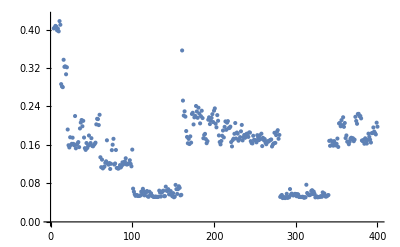

0.151125

21.3739

```mathematica
Clear[h1,h2,h3,h4];
TimeArray = {};
For[i=1,i≤20,i++,
For[j=1,j≤20,j++,
AppendTo[TimeArray,    Timing[  Calc[Simplify[Calc[  PartI[[i]]  PartII[[j]] ]]]  ][[1]]   ]
]
]//Timing
ListPlot[TimeArray]
Mean[TimeArray]
N[1/(60 60 24)Mean[TimeArray] Length[PartI]Length[PartII]]
Clear[TimeArray,h1,h2,h3,h4];
```

{102.24,Null}

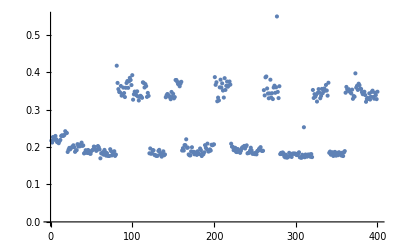

0.255578

16.0773

```mathematica
TimeArray = {};
h1=h2=h3=h4=1;
For[i=1,i≤20,i++,
For[j=1,j≤20,j++,
AppendTo[TimeArray,    Timing[  Calc[Simplify[Calc[  PartI[[i]]  PartII[[j]] ]]]  ][[1]]   ]
]
]//Timing
ListPlot[TimeArray]
Mean[TimeArray]
N[1/(60 60 24)Mean[TimeArray] Length[PartI]Length[PartII]]
Clear[TimeArray,h1,h2,h3,h4];
```

```mathematica
PartialSum = 0;
Parallelize[
Sum[Calc[Simplify[Calc[  PartI[[i]]  PartII[[j]] ]]],{i,1,3},{j,1,3}];
Sum[Calc[Simplify[Calc[  PartI[[i]]  PartII[[j]] ]]],{i,4,6},{j,1,3}];
]//Timing
```

$Aborted